# Gravitational Perturbation Theory Chapter : 1

Contents of the Chapter 1

1. Geodesic Equations from a Variational Principle
2. Geodesics in Static, Spherically Symmetric Spacetimes
3. Schwarzschild Black Holes
      • Circular Geodesics in the Schwarzschild Metric
      • The Critical Impact Parameter
4. Order and Chaos in Geodesic Motion
      • Lyapunov Exponents for Circular Orbits

## Geodesic Equations

```mathematica
coords={t[λ],r[λ],θ[λ],ϕ[λ]};
dim=Length[coords];(*Calculate the inverse metric once to save computation time*)
```

```mathematica
g= {{-f[r[λ]],0,0,0},
              {0,1/h[r[λ]],0,0},
              {0,0,r[λ]^2,0},
              {0,0,0,(r [λ]Sin[θ[λ]])^2}};
```

```mathematica
g//TraditionalForm//FullSimplify
```

(2/(r(λ))-1 | 0 | 0 | 0
0 | 1/(h(r(λ))) | 0 | 0
0 | 0 | (r(λ))^2 | 0
0 | 0 | 0 | (r(λ))^2 sin^2(θ(λ)))

```mathematica
ginv=Simplify[Inverse[g]];
Christoffel=
Simplify[Table[1/2*Sum[ginv[[k,α]]*(D[g[[α,i]],coords[[j]]]+D[g[[α,j]],coords[[i]]]-D[g[[i,j]],coords[[α]]]),{α,1,dim}],{k,1,dim},{i,1,dim},{j,1,dim}]];
```

```mathematica
geodesics=Table[D[coords[[μ]],{λ,2}]+Sum[Christoffel[[μ,α,β]]*D[coords[[α]],λ]*D[coords[[β]],λ],{α,1,dim},{β,1,dim}],{μ,1,dim}];
```

```mathematica
TableForm[Table[geodesics[[i]]==0,{i,1,4}]]
```

(2 r'[λ] t'[λ])/((-2+r[λ]) r[λ])+t''[λ]==0
-(h'[r[λ]] r'[λ]^2)/(2 h[r[λ]])+(h[r[λ]] t'[λ]^2)/r[λ]^2-h[r[λ]] r[λ] θ'[λ]^2-h[r[λ]] r[λ] Sin[θ[λ]]^2 ϕ'[λ]^2+r''[λ]==0
(2 r'[λ] θ'[λ])/r[λ]-Cos[θ[λ]] Sin[θ[λ]] ϕ'[λ]^2+θ''[λ]==0
(2 r'[λ] ϕ'[λ])/r[λ]+2 Cot[θ[λ]] θ'[λ] ϕ'[λ]+ϕ''[λ]==0

#### Let’s look the equations individually

```mathematica
equatorialGeodesics=geodesics/. {θ[λ]->π/2,θ'[λ]->0,θ''[λ]->0}//Simplify;
```

```mathematica
equatorialGeodesics[[1]]
```

(2 r'[λ] t'[λ])/((-2+r[λ]) r[λ])+t''[λ]

```mathematica
equatorialGeodesics[[1]]*f[r[λ]]//FullSimplify
```

(2 r'[λ] t'[λ]+(-2+r[λ]) r[λ] t''[λ])/r[λ]^2

```mathematica
equatorialGeodesics[[4]]
```

(2 r'[λ] ϕ'[λ])/r[λ]+ϕ''[λ]

```mathematica
equatorialGeodesics[[4]]*r[λ]^2//FullSimplify
```

r[λ] (2 r'[λ] ϕ'[λ]+r[λ] ϕ''[λ])

```mathematica
rules={t'[λ]->E0/f[r[λ]],ϕ'[λ]->L/r[λ]^2};
```

```mathematica
norm=-f[r[λ]] t'[λ]^2+r'[λ]^2/h[r[λ]]+r[λ]^2 ϕ'[λ]^2;

normEq=norm==-κ;

radialFirst=Simplify[normEq/. {t'[λ]->E0/f[r[λ]],ϕ'[λ]->L/r[λ]^2}]
```

κ+L^2/r[λ]^2+(E0^2 r[λ])/(2-r[λ])+r'[λ]^2/h[r[λ]]==0

#### Effective potential to study the geodesics in case of Schwarzschild Black holes

For k=1 (Massive particles)

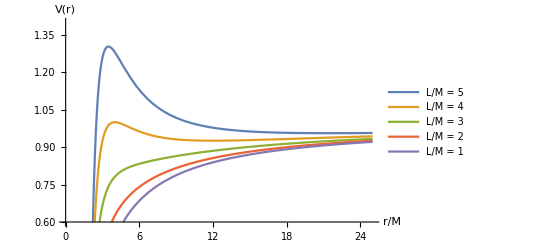

```mathematica
M=1;

Veff[L_,r_]:=(1-2 M/r) (1+L^2/r^2);

Plot[{Veff[5 M,r],Veff[4 M,r],Veff[3 M,r],Veff[2 M,r],Veff[M,r]},{r,2.01 M,25 M},PlotRange->{0.6,1.4},AxesLabel->{"r/M","V(r)"},PlotLegends->{"L/M = 5","L/M = 4","L/M = 3","L/M = 2","L/M = 1"}]
```

For k=0 (Massless particles)

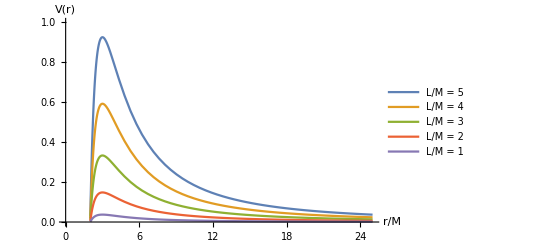

```mathematica
M=1;

Veff[L_,r_]:=(1-2 M/r) (L^2/r^2);

Plot[{Veff[5 M,r],Veff[4 M,r],Veff[3 M,r],Veff[2 M,r],Veff[M,r]},{r,2.01 M,25 M},PlotRange->{0,1},AxesLabel->{"r/M","V(r)"},PlotLegends->{"L/M = 5","L/M = 4","L/M = 3","L/M = 2","L/M = 1"}]
```

```mathematica
Export["/Users/gaurav/Documents/Project Work/Masters thesis /Thesis write up /Images /chapter 1/V_effective_photon.pdf",%53,"PDF"]
```

/Users/gaurav/Documents/Project Work/Masters thesis /Thesis write up /Images /chapter 1/V_effective_photon.pdf

```mathematica
Clear[k, EffectivePotential, L]
```

```mathematica
EffectivePotential[k_,r_] :=(1-2 M/r) (k+L^2/r^2);
```

```mathematica
Solve[D[EffectivePotential[1,r],r]==0,r] (*For Massive Particles*)
```

{{r→ConditionalExpression[6, ]},{r→ConditionalExpression[-1/2 Im[True]^2+1/2 √(12 Im[True]^2+Im[True]^4), (Re[True]==0&&Im[True]>0)||(Re[True]==0&&Im[True]<0)]},{r→ConditionalExpression[Re[True]^2/2-1/2 √(-12 Re[True]^2+Re[True]^4), ]},{r→ConditionalExpression[Re[True]^2/2+1/2 √(-12 Re[True]^2+Re[True]^4), ]}}

```mathematica
Solve[D[EffectivePotential[0,r],r]==0,r](*For Massless Particles*)
```

Solve::fdimc: When parameter values satisfy the condition L==0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{{r→ConditionalExpression[3, (Im[True]==0&&Re[True]>0)||(Im[True]==0&&Re[True]<0)||Im[True]>0||Im[True]<0]}}

```mathematica
D[EffectivePotential[k,r],{r,2}]//FullSimplify
```

(6 L^2 (-4+r)-4 k r^2)/r^5

```mathematica
Solve[D[EffectivePotential[k,r],r]==0,L] (*For Massive Particles*)
```

Solve::naqs: -(2 L^2 (1-2/r))/r^3+(2 (k+L^2/r^2))/r^2==0&&L&&r>0&&r>0 is not a quantified system of equations and inequalities.

Solve::naqs: -(2 L^2 (1-2/r))/r^3+(2 (k+L^2/r^2))/r^2==0&&L is not a quantified system of equations and inequalities.

Solve[-(2 L^2 (1-2/r))/r^3+(2 (k+L^2/r^2))/r^2==0,L]

```mathematica
L=(√k)/(√(-3/r^2+1/r));
```

```mathematica
(6 L^2 (-4+r)-4 k r^2)/r^5//FullSimplify
```

(2 k (-6+r))/((-3+r) r^3)

```mathematica
Vdoubleder[r_]:=(2 k (-6+r))/((-3+r) r^3);
```

```mathematica
k=1;
```

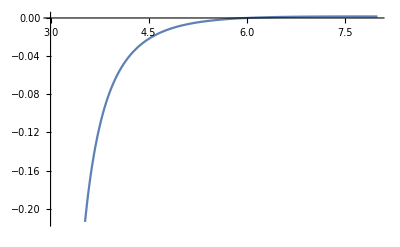

```mathematica
Plot[Vdoubleder[r],{r,3,8}]
```

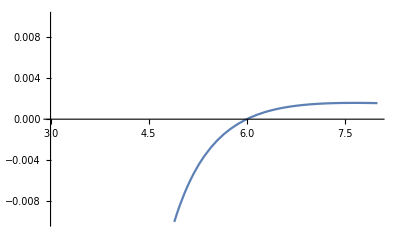

```mathematica
Plot[Vdoubleder[r],{r,3,8},PlotRange->{
-0.01,0.01}]
```

#### Impact Parameter

```mathematica
KE= 1- EffectivePotential[k,r]
```

1-(1+1/((-3/r^2+1/r) r^2)) (1-2/r)

```mathematica
Clear[L, r, k]
```

```mathematica
M=1;
k=1;
```

```mathematica
FullSimplify[Solve[KE==0,r]]
```

{{r→4}}

```mathematica
L=4 ;
```

```mathematica
FullSimplify[Solve[KE==0,r]](*Marginally bound orbit*)
```

```mathematica
Clear[L,r]
```

```mathematica
k=0;
```

```mathematica
KE
```

1-(1+1/((-3/r^2+1/r) r^2)) (1-2/r)

```mathematica
Solve[D[KE*r^3,r]==0,L]//FullSimplify
```

Solve::naqs: 3 (1-(1+Times[«2»]) (1+Times[«2»])) r^2+(-((Times[«3»]+Times[«4»]) (1+Times[«2»]))-(2 (1+Times[«2»]))/r^2) r^3==0&&L&&r>0&&r>0 is not a quantified system of equations and inequalities.

Solve::naqs: 3 (1-(1+Times[«2»]) (1+Times[«2»])) r^2+(-((Times[«3»]+Times[«4»]) (1+Times[«2»]))-(2 (1+Times[«2»]))/r^2) r^3==0&&L is not a quantified system of equations and inequalities.

{}

```mathematica
KE*r^3/.L->√3 r//FullSimplify
```

((-4+r) r^2)/(-3+r)

∴ We can see that r = 3 and L=3 √3

```mathematica
KE
```

1-(1+1/((-3/r^2+1/r) r^2)) (1-2/r)

#### Visualizing the impact parameter

```mathematica
M=1;

poly[r_,b_]:=r^3-b^2 r+2 M b^2;

Manipulate[Plot[poly[r,b],{r,-2,10},PlotRange->{-50,100},AxesLabel->{"r","r^3 - b^2 r + 2 M b^2"},Epilog->{Red,PointSize[Large],Point[{#,0}&/@(r/. NSolve[poly[r,b]==0,r])]}],{b,2,7}]
```

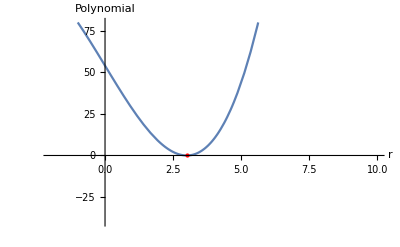

```mathematica
bcrit=3 Sqrt[3];

Plot[poly[r,bcrit],{r,-2,10},PlotRange->{-40,80},AxesLabel->{"r","Polynomial"},Epilog->{Red,PointSize[Large],Point[{3,0}]}]
```

### Lyapunov calculation for double pendulum

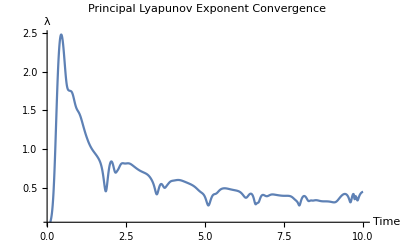

```mathematica
(*1. Parameters*)g=9.81;m1=1;m2=1;l1=1;l2=1;

(*2. Hamiltonian& Jacobian*)
vars={θ1[t],θ2[t],p1[t],p2[t]};
T=(m2 l2^2 p1[t]^2+(m1+m2) l1^2 p2[t]^2-2 m2 l1 l2 p1[t] p2[t] Cos[θ1[t]-θ2[t]])/(2 l1^2 l2^2 m2 (m1+m2 Sin[θ1[t]-θ2[t]]^2));
V=-(m1+m2) g l1 Cos[θ1[t]]-m2 g l2 Cos[θ2[t]];
H=T+V;

forceField={D[H,p1[t]],D[H,p2[t]],-D[H,θ1[t]],-D[H,θ2[t]]};
K=Outer[D,forceField,vars];

(*3. Deviation Vector Setup (4 equations instead of 16)*)
devVars={d1[t],d2[t],d3[t],d4[t]};
devEqs=Thread[D[devVars,t]==K.devVars];

(*4. Solve*)
tMax=10;
initialOrbit={θ1[0]==1.5,θ2[0]==1.5,p1[0]==0,p2[0]==0};
initialDev={d1[0]==10^-6,d2[0]==0,d3[0]==0,d4[0]==0};

sol=NDSolve[Join[Thread[D[vars,t]==forceField],devEqs,initialOrbit,initialDev],Join[vars,devVars],{t,0,tMax},MaxSteps->10^6];

(*5. Calculate Lambda*)
dVec[t_]:={d1[t],d2[t],d3[t],d4[t]}/. sol[[1]];
d0=Norm[{10^-6,0,0,0}];
lambda[t_]:=(1/t)*Log[Norm[dVec[t]]/d0];

Plot[lambda[t],{t,0.1,tMax},PlotRange->All,AxesLabel->{"Time","λ"},PlotLabel->"Principal Lyapunov Exponent Convergence"]
```

D::dvar: Multiple derivative specifier {t,2.01012,χ,ϕ} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::ivar: 2.01012 is not a valid variable.

D::dvar: Multiple derivative specifier {t,2.01012,χ,ϕ} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::ivar: 2.01012 is not a valid variable.

D::dvar: Multiple derivative specifier {t,2.01012,χ,ϕ} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

General::stop: Further output of D::dvar will be suppressed during this calculation.

General::ivar: 2.01012 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

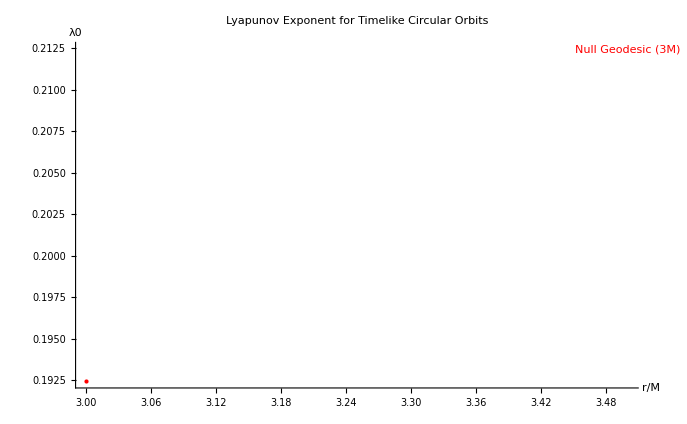

```mathematica
(*Schwarzschild Metric Parameters*)M=1;
f[r_]:=1-(2 M)/r;
h[r_]:=f[r];(*In Schwarzschild,g^rr=g_tt=f*)(*1. Second Derivative of Potential for Timelike Geodesics*)(*Using Eq.2.4.69 from your text*)f1[r_]:=D[f[x],x]/. x->r;
f2[r_]:=D[f[x],{x,2}]/. x->r;

Vr2[r_]:=2 h[r] (f[r]/r^2) ((-3 f[r] f1[r]/r+2 f1[r]^2-f[r] f2[r])/(2 f[r]-r f1[r]));

(*2. Lyapunov Exponent lambda0 (Eq.2.4.71)*)
lambdaTimelike[r_]:=Sqrt[Max[0,1/2 (2 f[r]-r f1[r]) Vr2[r]]];

(*3. Null Geodesic Value (Single Point at r=3M)*)
lambdaNull=1/(Sqrt[3] 3 M);(*Analytical value for Schwarzschild*)(*4. Plotting*)Plot[lambdaTimelike[r],{r,2.01 M,8 M},PlotRange->All,Filling->Axis,PlotStyle->{Thick,Blue},AxesLabel->{"r/M","λ0"},PlotLabel->"Lyapunov Exponent for Timelike Circular Orbits",Epilog->{Red,PointSize[Large],Point[{3 M,lambdaNull}],Text["Null Geodesic (3M)",{3.5 M,lambdaNull+0.02}]}]
```

Numerical evaluated value at 3M: 1/(3 √3)

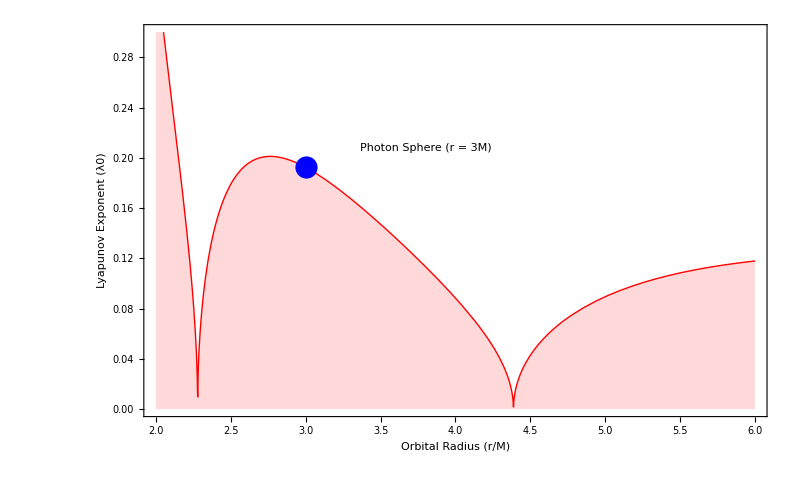

```mathematica
(*1. Clear previous definitions to prevent conflicts*)ClearAll["Global`*"];

M=1;
f[r_]:=1-2*M/r;
Veff[r_]:=f[r]/r^2;

(*2. Pre-calculate the derivatives symbolically ONCE*)
(*Notice we use "=" instead of ":=" so it evaluates immediately*)
d2VdrStar2[r_]=Simplify[f[r]*D[f[x]*D[Veff[x],x],x]/. x->r];

(*3. Define the Lyapunov function*)
lambdaNullFunc[r_]=Simplify[1/Sqrt[2]*Sqrt[Abs[-(r^2/f[r])*d2VdrStar2[r]]]];

(*4. Evaluate at the peak*)
rc=3*M;
lambdaPeak=lambdaNullFunc[rc];

Print["Numerical evaluated value at 3M: ",lambdaPeak];

(*5. Plot*)
Plot[lambdaNullFunc[r],{r,2.0*M,6*M},PlotRange->{{2.0*M,6*M},{0,0.3}},PlotStyle->{Thick,Red},Filling->Axis,FillingStyle->Directive[Red,Opacity[0.15]],(*Professional Formatting*)Frame->True,FrameLabel->{Style["Orbital Radius (r/M)",14],Style["Lyapunov Exponent (λ0)",14]},BaseStyle->{FontSize->12,FontFamily->"Times"},(*Highlight the Photon Sphere*)GridLines->{{rc},{lambdaPeak}},GridLinesStyle->Directive[Gray,Dashed],Epilog->{{Blue,PointSize[0.02],Point[{rc,lambdaPeak}]},Inset[Framed[Style["Photon Sphere (r = 3M)",11,Bold,Black],Background->LightYellow,FrameStyle->Blue],{rc+0.8,lambdaPeak+0.015}]}]
```